```mathematica
denom[a_,b_,xlower_,xupper_,ylower_,yupper_]:=NIntegrate[1/(1+(a - x)^2 + b(y - x^2)^2),{x,xlower,xupper},{y,ylower, yupper},AccuracyGoal->Infinity,MaxRecursion->100000,MaxPoints->10000000]
```

```mathematica
denom[1,100,-2,4,-1,12]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.05461

```mathematica
NumberForm[1.0546134367037538,16]
```

1.054613436703754

```mathematica
NumberForm[1.0546134367037538,16]
```

1.054613436703754

```mathematica
fUnnormalisedRosenbrock[x_,y_,a_,b_]:=((a - x)^2 + b(y - x^2)^2)
```

```mathematica
fUnnormalisedRosenbrock[10, 10, 1, 100]
```

810081

```mathematica
fUnnormalisedRosenbrockLogPDF[x_,y_,a_,b_]:=Log[1 / (1+((a - x)^2 + b(y - x^2)^2))]
```

```mathematica
fUnnormalisedRosenbrockLogPDF[1, 1, 1,100]
```

0

```mathematica
N@D[fUnnormalisedRosenbrockLogPDF[x, y, 1, 100],x]/.{x->3, y->4}
```

-2.39681

```mathematica
fUnnormalisedRosenbrockLogPDF[0.5,6,1,100]
```

-8.10395

```mathematica
(1 + fUnnormalisedRosenbrock[0.5,6,1,100])
```

3307.5

```mathematica
NumberForm[0.0003023431594860166,16]
```

0.0003023431594860166

```mathematica
N[-Log[810082]]
```

-13.6049

```mathematica
fRosenbrockPDF[x_,y_,a_,b_,xlower_,xupper_,ylower_,yupper_]:=1/(1+(a - x)^2 + b(y - x^2)^2) / denom[a,b,xlower,xupper,ylower,yupper]
```

```mathematica
NIntegrate[(x-0.87)(y- 2.6)fRosenbrockPDF[x,y,1,100,-2,4,-1,12],{x,-2,4},{y,-1,12},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.70258

```mathematica
NIntegrate[(y-2.60)^2 fRosenbrockPDF[x,y,1,100,-2,4,-1,12],{x,-2,4},{y,-1,12},AccuracyGoal->Infinity]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8.52658

```mathematica
D[Log[1/(1+(a - x)^2 + b(y - x^2)^2) ],x]
```

-(-2 (a-x)-4 b x (-x^2+y))/(1+(a-x)^2+b (-x^2+y)^2)

```mathematica
D[Log[1/(1+(a - x)^2 + b(y - x^2)^2) ],y]
```

-(2 b (-x^2+y))/(1+(a-x)^2+b (-x^2+y)^2)

```mathematica
1/(1.0546134367037538(1+(1 - x)^2 + 100(y - x^2)^2))
```

```mathematica
ContourPlot[fRosenbrockPDF[x,y,1,100],{x,-2,4},{y,-1,12},Contours->200,PlotRange->Full,PlotPoints->100]
```

-Graphics-

```mathematica
D[RealAbs[x],x]/.{x->0}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Norm[{x,y}]
```

```mathematica
D[(√(x^2+y^2+z^2))^β,x]
```

x (x^2+y^2+z^2)^(-1+β/2) β

```mathematica
fConeLogDeriv[x__,β_]:=Block[{cons=β(Norm[x]^2)^(-1 + β /2)},-Table[cons * x[[i]],{i,1,Length@x,1}]]
```

```mathematica
fConeLogDeriv[{-1,3},1]
```

{1/(√10),-3/(√10)}

```mathematica
-Norm[{-1,3}]
```

-√10

```mathematica
Norm[{-1,3,2,4,5,6,7,8,9,10}]^2
```

385

```mathematica
0.3 385^(-1 + 0.15)
```

0.00190318

```mathematica
fConeLogDeriv[{-1,3,2,4,5,6,7,8,9,10},0.3]
```

{0.00190318,-0.00570954,-0.00380636,-0.00761272,-0.00951589,-0.0114191,-0.0133223,-0.0152254,-0.0171286,-0.0190318}

```mathematica
N@Abs'[1]
```

Abs'[1.]

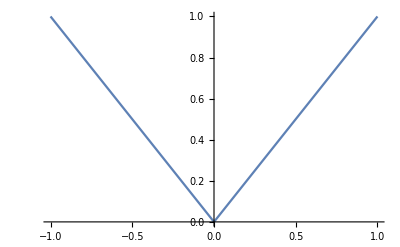

```mathematica
Plot[Abs[x],{x,-1,1}]
```

```mathematica
D[Abs'[x], x]
```

Abs''[x]

```mathematica
D[-(Sqrt[x^2+y^2] - r)^2 / (2 σ^2),y]
```

```mathematica
-(x(-r+√(x^2+y^2)))/(√(x^2+y^2) σ^2)/.{x->0, y->-9,r->10,σ->1}
```

0

```mathematica
-(y (-r+√(x^2+y^2+z^2)))/(√(x^2+y^2+z^2) σ^2)
```

```mathematica
D[-(Sqrt[x^2+y^2+z^2] - r)^2 / (2 σ^2),y]
```

```mathematica
-(y (-r+√(x^2+y^2+z^2)))/(√(x^2+y^2+z^2) σ^2)
```

```mathematica
fDerivAnnulus[x__,r_,σ_]:=Block[{cons=-(Norm[x] - r) / (Norm[x] σ^2)},Table[cons x[[i]],{i,1,Length@x,1}]]
```

```mathematica
fDerivAnnulus[{0,-9},10, 1]
```

{0,-1}

```mathematica
fDerivAnnulus[{2,-1,1,3},20,3]
```

{(2 (20-√15))/(9 √15),-(20-√15)/(9 √15),(20-√15)/(9 √15),(20-√15)/(3 √15)}

```mathematica
N@Exp[-(Norm[{0,-9}]-10)^2/(2)]
```

0.606531

```mathematica
D[Log[PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}] + PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}]],x]
```

-ⅇ^(1/2 (-x^2-y^2)+1/2 (x^2+y^2)) x

```mathematica
FullSimplify@D[Log@PDF[MultinormalDistribution[{a,b},IdentityMatrix[2]],{x,y}]+
Log@PDF[MultinormalDistribution[{c,d},{{3,0.5},{0.5,2}}],{x,y}],y]
```

b-0.0869565 c+0.521739 d+0.0869565 x-1.52174 y

```mathematica
FullSimplify@Log[PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}]]
```

Log[(ⅇ^(-x^2/2-y^2/2))/(2 π)]

```mathematica
fTest[x1_,y1_]:=Exp[Log@PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}] +Log@PDF[MultinormalDistribution[{10,10},IdentityMatrix[2]],{x,y}] ]/.{x->x1,y->y1}
```

```mathematica
N@fTest[1,0]
```

7.63559×10^-42

```mathematica
FullSimplify@FunctionExpand@Log@PDF[MultinormalDistribution[{10,10},IdentityMatrix[2]],{x,y}]
```

Log[ⅇ^(-1/2 (-10+x)^2-1/2 (-10+y)^2)]-Log[2 π]

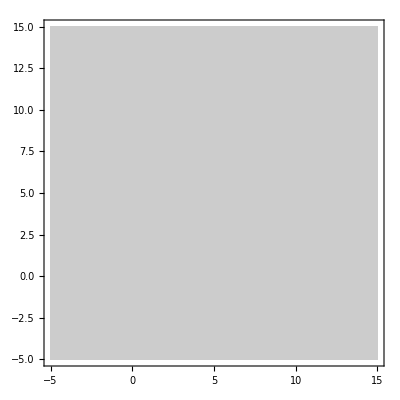

```mathematica
ContourPlot[Exp[Log@PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],{x,y}] +Log@PDF[MultinormalDistribution[{10,10},IdentityMatrix[2]],{x,y}]],{x,-5,15},{y,-5,15},PlotRange->Full]
```

```mathematica
{{2,0.5,-0.1},{0.2,1,0.4},{-0.1,0.4,3}}//MatrixForm
```

(2 | 0.5 | -0.1
0.2 | 1 | 0.4
-0.1 | 0.4 | 3)

```mathematica
D[PDF[MultinormalDistribution[{a,b,c},{{2,0.5,-0.1},{0.5,1,0.4},{-0.1,0.4,3}}],{x,y,z}],x]
```

0.0143711 ⅇ^(1/2 (-(-b+y) (-0.315574 (-a+x)+1.22746 (-b+y)-0.17418 (-c+z))-(-a+x) (0.581967 (-a+x)-0.315574 (-b+y)+0.0614754 (-c+z))-(-c+z) (0.0614754 (-a+x)-0.17418 (-b+y)+0.358607 (-c+z)))) (-1.16393 (-a+x)+0.631148 (-b+y)-0.122951 (-c+z))

```mathematica
PositiveDefiniteMatrixQ[{{1,0},{0,1}}]
```

True

```mathematica
Assuming[PositiveDefiniteMatrixQ[Σ],D[PDF[MultinormalDistribution[{a,b,c, d},Σ],{x,y,z,w}],x]]
```

PDF^(0,{1,0,0,0})[MultinormalDistribution[{a,b,c,d},Σ],{x,y,z,w}]

```mathematica
D[Log@PDF[MultinormalDistribution[{a,b,c},{{2,0.5,-0.1},{0.5,1,0.4},{-0.1,0.4,3}}],{x,y,z}],x]
```

0.5 ⅇ^(1/2 (-(-b+y) (-0.315574 (-a+x)+1.22746 (-b+y)-0.17418 (-c+z))-(-a+x) (0.581967 (-a+x)-0.315574 (-b+y)+0.0614754 (-c+z))-(-c+z) (0.0614754 (-a+x)-0.17418 (-b+y)+0.358607 (-c+z)))+1/2 ((-b+y) (-0.315574 (-a+x)+1.22746 (-b+y)-0.17418 (-c+z))+(-a+x) (0.581967 (-a+x)-0.315574 (-b+y)+0.0614754 (-c+z))+(-c+z) (0.0614754 (-a+x)-0.17418 (-b+y)+0.358607 (-c+z)))) (-1.16393 (-a+x)+0.631148 (-b+y)-0.122951 (-c+z))

```mathematica
fMultimodal[x_,y_,z_,mu1x_,mu1y_,mu1z_,mu2x_,mu2y_,mu2z_,sigma1x_,sigma1y_,sigma1z_,rho1xy_,rho1xz_,rho1yz_,sigma2x_,sigma2y_,sigma2z_,rho2xy_,rho2xz_,rho2yz_]:=PDF[MultinormalDistribution[{mu1x,mu1y,mu1z},{{sigma1x^2,sigma1x sigma1y rho1xy, sigma1x sigma1z rho1xz},{sigma1x sigma1y rho1xy, sigma1y^2,sigma1y sigma1z rho1yz},{sigma1x sigma1z rho1xz, sigma1y sigma1z rho1yz,sigma1z^2}}],{x,y,z}]+PDF[MultinormalDistribution[{mu2x,mu2y,mu2z},{{sigma2x^2,sigma2x sigma2y rho2xy, sigma2x sigma2z rho2xz},{sigma2x sigma2y rho2xy, sigma2y^2,sigma2y sigma2z rho2yz},{sigma2x sigma2z rho2xz, sigma2y sigma2z rho2yz,sigma2z^2}}],{x,y,z}]
```

```mathematica
D[Log@fMultimodal[x,y,z,1,2,3,3,4,5,5,3,2,0.5,-0.1,0.4,5,6,7,0.3,0.2,-0.3],z]/.{x->2,y->4,z->5}
```

-0.393172

```mathematica
fAnalyticDeriv[x_,y_,z_,mu1x_,mu1y_,mu1z_,mu2x_,mu2y_,mu2z_,sigma1x_,sigma1y_,sigma1z_,rho1xy_,rho1xz_,rho1yz_,sigma2x_,sigma2y_,sigma2z_,rho2xy_,rho2xz_,rho2yz_]:=Block[{denom=fMultimodal[x,y,z,mu1x,mu1y,mu1z,mu2x,mu2y,mu2z,sigma1x,sigma1y,sigma1z,rho1xy,rho1xz,rho1yz,sigma2x,sigma2y,sigma2z,rho2xy,rho2xz,rho2yz]},-(1/ denom) (Inverse[{{sigma1x^2,sigma1x sigma1y rho1xy, sigma1x sigma1z rho1xz},{sigma1x sigma1y rho1xy, sigma1y^2,sigma1y sigma1z rho1yz},{sigma1x sigma1z rho1xz, sigma1y sigma1z rho1yz,sigma1z^2}}] .({x,y,z}-{mu1x,mu1y,mu1z})PDF[MultinormalDistribution[{mu1x,mu1y,mu1z},{{sigma1x^2,sigma1x sigma1y rho1xy, sigma1x sigma1z rho1xz},{sigma1x sigma1y rho1xy, sigma1y^2,sigma1y sigma1z rho1yz},{sigma1x sigma1z rho1xz, sigma1y sigma1z rho1yz,sigma1z^2}}],{x,y,z}]+Inverse[{{sigma2x^2,sigma2x sigma2y rho2xy, sigma2x sigma2z rho2xz},{sigma2x sigma2y rho2xy, sigma2y^2,sigma2y sigma2z rho2yz},{sigma2x sigma2z rho2xz, sigma2y sigma2z rho2yz,sigma2z^2}}] .({x,y,z}-{mu2x,mu2y,mu2z})PDF[MultinormalDistribution[{mu2x,mu2y,mu2z},{{sigma2x^2,sigma2x sigma2y rho2xy, sigma2x sigma2z rho2xz},{sigma2x sigma2y rho2xy, sigma2y^2,sigma2y sigma2z rho2yz},{sigma2x sigma2z rho2xz, sigma2y sigma2z rho2yz,sigma2z^2}}],{x,y,z}])]
```

```mathematica
fAnalyticDeriv[2,4,5,1,2,3,3,4,5,5,3,2,0.5,-0.1,0.4,5,6,7,0.3,0.2,-0.3]
```

{-0.0247543,-0.0549335,-0.393172}